```mathematica
par0[x_]=a*x^2+b*x+c
```

c+b x+a x^2

```mathematica
sh=Solve[par0[0]==h,{a,b,c}]
```

{{c→h}}

```mathematica
par1[x_]=par0[x]/.sh[[1]]
```

h+b x+a x^2

```mathematica
stheta=Solve[par1'[0]==Cos[2*theta]/Sin[2*theta],{a,b}]
```

{{b→Cot[2 theta]}}

```mathematica
par2[x_]=par1[x]/.stheta[[1]]
```

h+a x^2+x Cot[2 theta]

```mathematica
szero=Solve[par2'[x]==0,{x}]
```

{{x→-Cot[2 theta]/(2 a)}}

```mathematica
hmax=par2[x/.szero[[1]]]
```

h-Cot[2 theta]^2/(4 a)

```mathematica
g=10;
eh[h_]:=g*h;
ev[v_]:=(v^2)/2;
ve[e_]:=Sqrt[2*e];
heq=(hmax==ev[ve[eh[d-h]]*Cos[2*theta]]/g+h)
```

h-Cot[2 theta]^2/(4 a)==h+(d-h) Cos[2 theta]^2

```mathematica
se=Solve[heq,a]
```

{{a→-Csc[2 theta]^2/(4 (d-h))}}

```mathematica
par[x_]=par2[x]/.se[[1]]
```

h+x Cot[2 theta]-(x^2 Csc[2 theta]^2)/(4 (d-h))

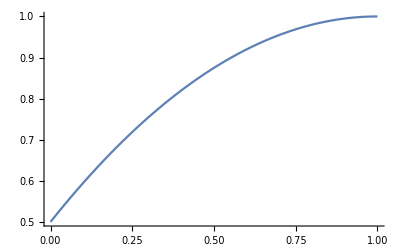

```mathematica
Plot[par[x]/.{d->3/2,h->1/2,theta->Pi/8},{x,0,1}]
```

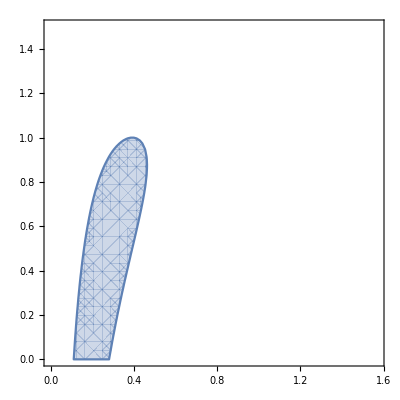

```mathematica
RegionPlot[(par[1]/.{d->3/2})>1,{theta,0,Pi/2},{h,0,3/2}]
```

```mathematica
sd=Solve[par[1]==1,d]
```

{{d→(-4 h+4 h^2+4 h Cot[2 theta]+Csc[2 theta]^2)/(4 (-1+h+Cot[2 theta]))}}

```mathematica
dmin=d/.sd[[1]]
```

(-4 h+4 h^2+4 h Cot[2 theta]+Csc[2 theta]^2)/(4 (-1+h+Cot[2 theta]))

```mathematica
Plot3D[If[dmin>h,dmin],{theta,0,Pi/2},{h,0,3/2}]
```

-Graphics3D-

```mathematica
fdmin[at_]=dmin/.theta->at
```

(-4 h+4 h^2+4 h Cot[2 at]+Csc[2 at]^2)/(4 (-1+h+Cot[2 at]))

```mathematica
shmin=Solve[fdmin'[theta]==0,h]
```

{{h→1/2 Csc[2 theta] Sec[2 theta] (-Cos[4 theta]+Sin[4 theta])}}

```mathematica
h/.shmin[[1]]
```

1/2 Csc[2 theta] Sec[2 theta] (-Cos[4 theta]+Sin[4 theta])

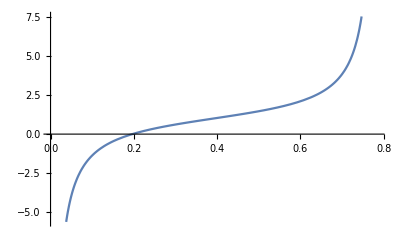

```mathematica
Plot[h/.shmin[[1]],{theta,0,Pi/4}]
```